# Visualizing Chaos

## Introduction

This notebook is intended to briefly explain how to produce Poincare plots, bifurcation diagrams, frequency spectrum plots, etc, in Mathematica for chaotic systems. The differential equations of the driven pendulum are used as an example; it is straightforward to modify the code to use different equations. Some of the explanations assume a basic knowledge of NDSolve interpolating functions; if you get confused or don't know what they are, refer to the seperate notebook file explaining them.

## Poincare Plots

Poincare plots are essentially by taking periodic 'slices' of phase space, and then adding all of the slices together. Dots are placed on the Poincare plot at the point where the trajectory passed through a given slice. In Mathematica, this process is realized using the Table function to generate an array of the points making up the Poincare plot, and then using ListPlot to plot the points.
 First, we have to obtain a numerical solution to the differential equation. The constants and form of the differential equation used below were chosen because they happen to produce a particularly attractive Poincare plot. The very large time range is necessary in order to generate a sufficient number of points for the Poincare plot.

```mathematica
q = 2;
g  = 1.50;
ω=2/3;

sol = NDSolve[{theta''[t] == - 1/q*theta'[t] - Sin[theta[t]] + g*Cos[ω t],
theta[0] == 0, theta'[0] == 0},{theta},{t, 0 ,50000}, MaxSteps -> 10000000]
```

{{theta→InterpolatingFunction[{{0.,50000.}},<>]}}

Now, use the Table function to create the array. This function behaves somewhat like a For loop - you specify a function for it to use to generate the values of the table (i.e., array) and an iterator variable that can serve as the argument of the function.

Next make a Phase Plot. Enter values from Figure 3.4 from Gollub & Baker; g = 1.07, q = 2, ω = 2/3, for example.

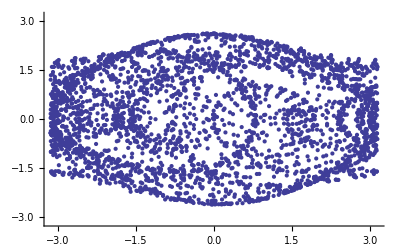

```mathematica
data=Table[{Mod[First[theta[i]/.sol]-Pi,2 Pi]-Pi,First[theta'[i]/.sol]},{i,1000,2000,0.03*2 Pi/ω}];ListPlot[data,PlotRange->{{-π,π},{-π,π}}]
```

Poincare Plot. The step size in this case is  2 π / ω, the angular drive period in dimensionless units. The Mod function is necessary because we want theta[t] to be 'reset' to zero every time the pendulum passes the angle 2 Pi. NDSolve didn't do this itself - it just kept adding 2 Pi to its value every time the pendulum made a full revolution. For an explanation of why the First[] functions are necessary, refer to the interpolating functions notebook.
Now it only remains to plot the points above. This is straightforward, using ListPlot:

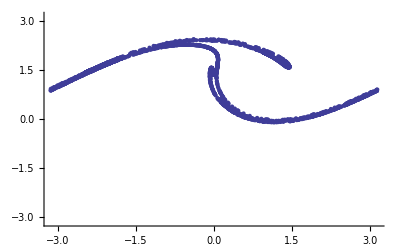

```mathematica
data=Table[{Mod[First[theta[i]/.sol]-Pi,2 Pi]-Pi,First[theta'[i]/.sol]},{i,1000 Pi/ω ,30000,2 Pi/ω}];ListPlot[data,PlotRange->{{-π,π},{-π,π}}]
```

Specifying several options, like the color and point size, can make the plot look better (although perhaps not increase its physical significance)

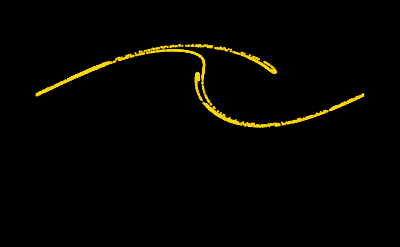

```mathematica
ListPlot[data,PlotStyle->{PointSize[.004],RGBColor[1,215/255,0]},Background->RGBColor[0,0,0],Axes->False,PlotRange->{{-π,π},{-π,π}}]
```

## Bifurcation Diagrams

Bifurcation diagrams illustrate the behavior of a chaotic system over a wide range of one of its parameters. They are constructed by first solving the differential equation(s) for multiple values of a given parameter, and then for each value, plotting the value of some dynamical variable at a set of discrete times (normally given by a drive frequency if one is present) against the varied parameter. In the case of the driven pendulum, either the drive frequency, amplitude, or damping coefficient can be varied, and the value of theta', the angular velocity, is plotted once every drive period. To create a bifurcation diagram in Mathematica, two For loops are used - one to cycle through different values of the varied parameter, and one to create an array of values of the angular velocity at different times for each value of the parameter. This code is shown below. 
First, declare constants. The gStart, tStart, etc variables are important to the appearance of the bifurcation diagram as well as the computation time - see below notes.

```mathematica
wd = 2/3;
period = 2Pi/wd
q = 4;

gStart = .95;
gEnd = 1.55;
gRes = .004;

tStart = 80;
tEnd = 100;
tRes = 1;

theta0 = 0;
thetaP0 = 0;
(gEnd - gStart)/gRes
```

3 π

150.

Now run the two For loops:

The following input cell could not be processed, possibly due to syntax error(s).

```mathematica
(* For each value of g... *)
For[i=0;g=gStart;array1={}, i≤(gEnd - gStart)/gRes, i++, g=gStart+gRes*i; 

(* Solve the differential equation... *)
sol=NDSolve[{theta''[t]+(1/q)theta'[t]+Sin[theta[t]]==g Cos[wd t],theta[0]==theta0,theta'[0]==thetaP0},
theta,{t,tStart*period, tEnd*period},MaxSteps->20000];

(* ...and create 40 values of theta'[t] *)
	For[j=tStart, j≤tEnd, j = j+tRes,array1 = Append[array1,{g,theta'[period* j]}/.sol[[1]]];
      ]
]
```

Unfortunately, because for any given initial conditions, only half of all possible angular velocities at a given value of g actually occur, this code must be run twice to produce the entire bifurcation diagram. This is illustrated below. First, there are several notes to be made about the above code:
1) The code takes a rather long time to run in Mathematica. This is because the differential equation must be solved hundreds of times (300 in the code above), corresponding to all of the different values of the drive amplitude, and then for each one of these values, the angular velocity must be recorded at many different times. Varying either g_res, t_start, t_end, or t_res will have a significant impact on the computation time. You will have to find a good balance between resolution (i.e., number of dots) and computation time. g_res controls the number of iterations of the parameter g, while t_res controls the number of time values plugged into theta'[t].
2) The time values inserted into theta'[t] do not start at zero in order to avoid deviant transient behavior of the trajectory before it 'finds' the attractor. The variable period is the drive period. It is crucial to the correct appearance of the bifurcation diagram that it be present.
3) The output of the code is stored in the array array1, as pairs of {g, theta'[t]} values.
Now, the code must be run once more, both resulting arrays plotted using ListPlot, and the plots added together. The code below assumes all of the constants above have been declared.

The following input cell could not be processed, possibly due to syntax error(s).

```mathematica
theta0 = 0;
thetaP0 = Pi;

(* For each value of g... *)
For[i=0;g=gStart;array2={}, i≤(gEnd - gStart)/gRes, i++, g=gStart+gRes*i; 

(* Solve the differential equation... *)
sol=NDSolve[{theta''[t]+(1/q)theta'[t]+Sin[theta[t]]==g Cos[wd t],theta[0]==theta0,theta'[0]==thetaP0},
theta,{t,tStart*period, tEnd*period},MaxSteps->22000];

(* ...and create 40 values of theta'[t] *)
	For[j=tStart, j≤tEnd, j = j+tRes,array2 = Append[array2,{g,theta'[period* j]}/.sol[[1]]];
      ]
]
```

Now, plot the results. Notice how in the plots of array1 and array2, only one of the two 'paths' after the bifurcations appear.

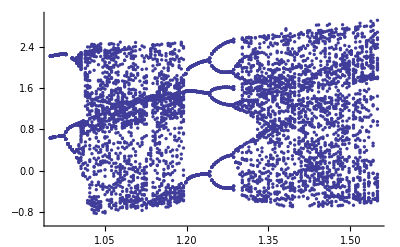

```mathematica
Show[ListPlot[array1,PlotStyle->{PointSize[.006]},PlotRange->{-1,3}],ListPlot[array2,PlotStyle->{PointSize[.006]},PlotRange->{-1,3}]]
```

## Frequency Spectrums

Frequency spectrums of time series are created using Mathematica's Fourier command. This command only operates on numerical data, so in order to use it on Interpolating functions, a table of datapoints must be created using the interpolating function. The driven pendulum equation with drive amplitude g = .95 is used as an example; the frequency spectrum of theta'[t] should reveal a spike at the drive frequency. 
First, solve the differential equation:

```mathematica
q = 4;
g  = 1.50;
ω=2/3;

sol = NDSolve[{theta''[t] + 1/q*theta'[t] + Sin[theta[t]] == g*Cos[ω t],
theta[0] == 0, theta'[0] == 0},{theta},{t, 20 ,100}, MaxSteps -> 30000]
```

{{theta→InterpolatingFunction[{{20.,100.}},<>]}}

Now generate a table of values of theta'[t].

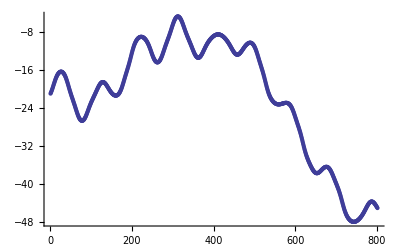

```mathematica
data = Table[ First[theta[t] /. sol],{t,20,100,.1}];
ListPlot[data]
```

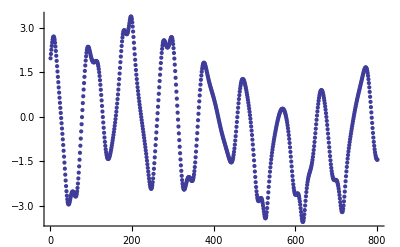

```mathematica
data = Table[ First[theta'[t] /. sol],{t,20,100,.1}];
ListPlot[data]
```

Now apply the Fourier command to the data. This generates a list of complex numbers. To make the plot come out nicely, it's best to take the log of the magnitude of the complex numbers, making the plot technically a plot of the power spectrum.

```mathematica
dataF = Abs[Fourier[data]];
```

To plot the data, one can either use ListPlot with an option to connect adjecent points enabled, or else one can create an interpolating function from the data. Both approaches are shown below. Only half of the data needs to be plotted because the Fourier transform of a list of numbers is symmetric about the center of the data set. However, in reality, the data plotted can be reduced even more if, as in this case, the frequency spikes end before the midpoint of the dataset. This is accomplished using Take, which takes the first n number of elements of the given array.

As of Version 6, PlotJoined has been superseded by Joined. »

ListPlot[Take[dataF,Round[Length[dataF]/2]],Joined→True,PlotRange→All]
ListPlot[Take[dataF,40],Joined→True,PlotRange→All]

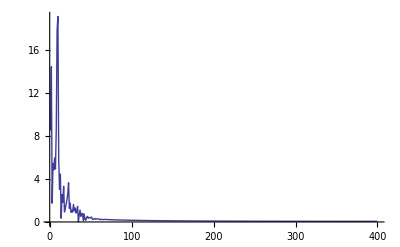

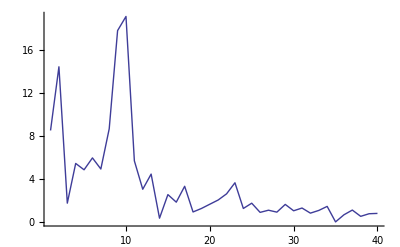

```mathematica
ListPlot[Take[dataF,Round[Length[dataF]/2]],PlotJoined->True,PlotRange->All]
ListPlot[Take[dataF,40],PlotJoined->True,PlotRange->All]
```

InterpolatingFunction[{{1.,801.}},<>]

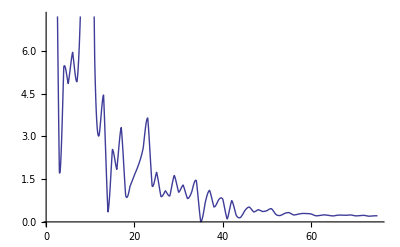

```mathematica
dataFif = Interpolation[dataF]
Plot[dataFif[t],{t,1,75}]
```

The spike around the 10th element of the transform appears to be relevant. To find out, we can transform the sine wave of the driving force, and plot both transforms on the same plot.

As of Version 6, PlotJoined has been superseded by Joined. »

drive=Table[1.5 Cos[ω t],{t,20,100,0.1}];
ListPlot[drive]
driveF=Abs[Fourier[drive]];
Show[ListPlot[Take[dataF,50],Joined→True,PlotRange→All],ListPlot[Take[driveF,50],Joined→True,PlotRange→All,PlotStyle→{RGBColor[1,0,0]}]]

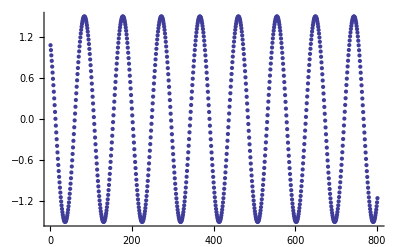

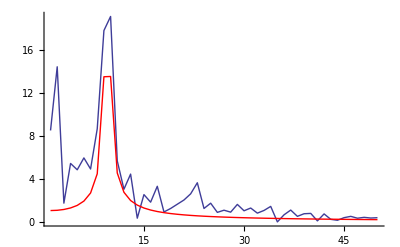

```mathematica
drive = Table[1.5Cos[ω t],{t,20,100,.1}];
ListPlot[drive]
driveF = Abs[Fourier[drive]];
Show[ListPlot[Take[dataF,50],PlotJoined->True,PlotRange->All],ListPlot[Take[driveF,50],PlotJoined->True,PlotRange->All,PlotStyle->{RGBColor[1,0,0]}]]
```

Clearly, the peak around the 10th element of the transform corresponds to the drive frequency. To verify this without creating a seperate plot of the drive amplitude, one can count the number of cycles of the drive frequency that occur during the total time spanned by the data set that is transformed. In the above case, the data set spans the time from t = 20 to 100. This is 80 time units, which, since the drive frequency is 1/3Pi Hz, means that 80/3Pi or about 8.5 drive cycles occur during this time. The spike in the frequency spectrum should then appear at around the (8.5 + 1)th element, which it does. 
To find the exact location of the peak, one can use an interpolating function and either FindMaximum or FindRoot:

```mathematica
dataFif = Interpolation[dataF];
FindMaximum[dataFif[t],{t,9}]
deriv = Derivative[1][dataFif];
FindRoot[deriv[t] ==0,{t,9}]
```

{19.9775,{t→9.63628}}

{t→9.63628}

The above procedure is a consequence of a general property of discrete Fourier transforms-that the index of a given point in the transformed data set corresponds to the amplitude of that frequency in the original data set which allows index minus one number of cycles to occur in the time spanned by the data set. There is a difference of one because the index starts at one instead of zero.